```mathematica
w = π/12;
```

```mathematica
g[h_]:= 0.44-0.46 Sin[0.9 + w h] + 0.11 Sin[0.9+2 w h]
```

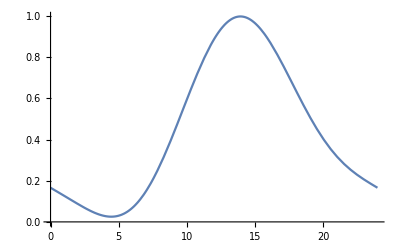

```mathematica
Plot[g[h],{h,0,24}]
```

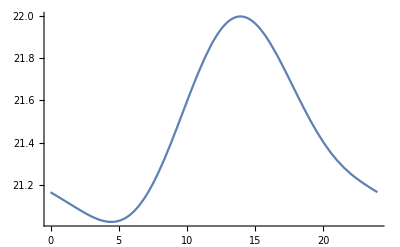

```mathematica
Tmax = 22; Tdiff = 1;
Ta[h_]:= Tmax - Tdiff(1-g[h]);
Plot[Ta[h],{h,0,24}]
```

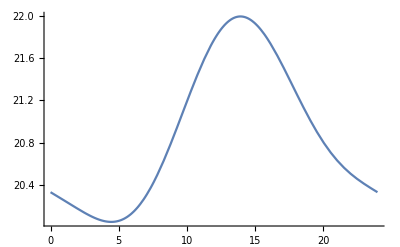

```mathematica
δ[j_]:= ArcSin[0.39795 Cos[0.21631 + 2 ArcTan[0.967 Tan[0.0086 (-186 + j)]]]]
```

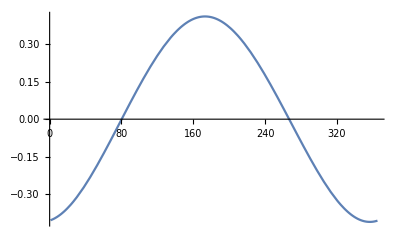

```mathematica
Plot[δ[j],{j,1,365}]
```

```mathematica
hday[ϕ_,δ_]:= 24 - 24/π ArcCos[(Sin[6 π/180]+ Sin[ϕ] Sin[δ])/(Cos[ϕ] Cos[δ])]
```

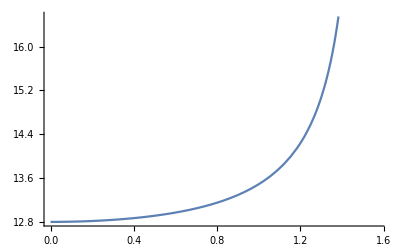

```mathematica
Plot[hday[a,0],{a,0,π/2}]
```

```mathematica
(*Solar declination*)
δ[J_]:= ArcSin[0.39785 Sin[(278.97 + 0.9856 J + 1.9165 Sin[(356.6 + 0.9856 J)DtoR])DtoR]]*1/DtoR
```

```mathematica
dat = Table[δ[j],{j,1,365}];
```

```mathematica
fit = NonlinearModelFit[dat, a Sin[b 2Pi / 365j - Pi/2],{a,b},j]
```

FittedModel[-22.7844 Cos[0.0178388 j]]

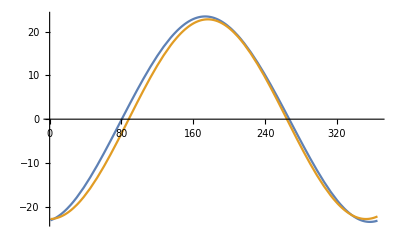

```mathematica
Plot[{δ[j],fit[j]},{j,1,365}]
```

```mathematica
(*Solar declination*)
sδ[J_]:= 0.39785 Sin[(278.97 + 0.9856 J + 1.9165 Sin[(356.6 + 0.9856 J)DtoR])DtoR]
```

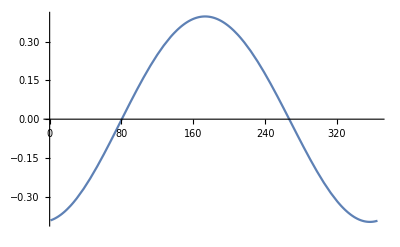

```mathematica
Plot[sδ[j],{j,1,365}]
```

```mathematica
(*Zenith angle as a function of time, latitude, and solar declination*)
DtoR = π/180;
cψ[t_,ϕ_, δ_]:=Sin[ϕ DtoR]Sin[δ DtoR] + Cos[ϕ DtoR] Cos[δ DtoR]Cos[(15(t-12))DtoR](*remove correciton here, assume that t0 = 12, we are on 0 longitude*)
```

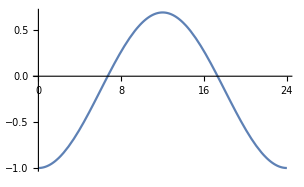

```mathematica
Plot[cψ[t,-23,23],{t,0,24}]
```

```mathematica
se=NSolve[cψ[t,-23,23]==0&& t≥ 0&& t≤ 24,t ]
```

{{t→6.69201},{t→17.308}}

```mathematica
se
```

{{t→6.69201},{t→17.308}}

```mathematica
t /. se[[2]]
```

17.308

```mathematica
.
```

```mathematica
(*Azimuth angle of the sun as a function of solar declination, and zenith angle*)
AZ[δ_,ψ_, ϕ_]:= -(Sin[δ DtoR] - Cos[ψ DtoR] Sin[ϕ DtoR])/(Cos[ϕ DtoR] Sin[ψ DtoR])
```

```mathematica
(*Position of the sun in the sky as a function of day of the year, time of the day, and latitude at longitude = 0*)
SolarRadiation[J_,t_,ϕ_]:= Module[{result,S0=1.361,sinδ,δ,cosδ, cosψ,sol,trise,tset,tt, DtoR = π/180,hs},
sinδ = 0.39785 Sin[(278.97 + 0.9856 J + 1.9165 Sin[(356.6 + 0.9856 J)DtoR])DtoR];
(*this is solar declination*)
δ = ArcSin[sinδ];
cosδ = Cos[δ];
cosψ[ti_]:=Sin[ϕ DtoR]sinδ + Cos[ϕ DtoR] cosδ Cos[(15.(ti-12))DtoR];

hs[δ_]:= ArcCos[(0 - Sin[ϕ DtoR]sinδ)/(Cos[ϕ DtoR] cosδ)]1/DtoR; 
(*cosψ disapears because we use geometric sunset*)
trise = 12- hs[δ]/15;
tset = 12 + hs[δ]/15;

If[t< trise || t > tset, 
result = 0,
result = S0 cosψ[t];
];
result]
```

```mathematica
(*Position of the sun in the sky as a function of day of the year, time of the day, and latitude at longitude = 0*)
SunRise[J_,ϕ_]:= Module[{result,sinδ,δ,cosδ, cosψ,sol,trise,tset,tt, DtoR = π/180,hs},
sinδ = 0.39785 Sin[(278.97 + 0.9856 J + 1.9165 Sin[(356.6 + 0.9856 J)DtoR])DtoR];
(*this is solar declination*)
δ = ArcSin[sinδ];
cosδ = Cos[δ];

hs[δ_]:= ArcCos[(0 - Sin[ϕ DtoR]sinδ)/(Cos[ϕ DtoR] cosδ)]1/DtoR; 
(*cosψ disapears because we use geometric sunset*)
trise = 12- hs[δ]/15;
result= Re@trise;
result]
```

```mathematica
SunRise[2,89]
```

12.

```mathematica
SolarRadiation[1,12,60]
```

164.066

```mathematica
31+28+20
```

79

```mathematica
asz =16 ; th = 1.5;
```

```mathematica
t1 = 172; t2 =79;
fig1a = Plot[{SolarRadiation[t1,t,60],SolarRadiation[t1,t,30],SolarRadiation[t1,t,0],SolarRadiation[t1,t,-30],SolarRadiation[t1,t,-60]},{t,0,24},PlotStyle->{{Blue},{Black},{Red},{Black,Dashed},{Blue,Dashed}},Ticks->{{0,3,6,9,12,15,18,21,24},Automatic},AxesStyle->Directive[asz,AbsoluteThickness[th],Black],ImageSize->Medium,PlotRange->{All,{0,1.4}}];

fig1b = Plot[{SolarRadiation[t2,t,60],SolarRadiation[t2,t,30],SolarRadiation[t2,t,0],SolarRadiation[t2,t,-30],SolarRadiation[t2,t,-60]},{t,0,24},PlotStyle->{{Blue},{Black},{Red},{Black,Dashed},{Blue,Dashed}},Ticks->{{0,3,6,9,12,15,18,21,24},Automatic},AxesStyle->Directive[asz,AbsoluteThickness[th],Black],ImageSize->Medium,PlotRange->{All,{0,1.4}}];
```

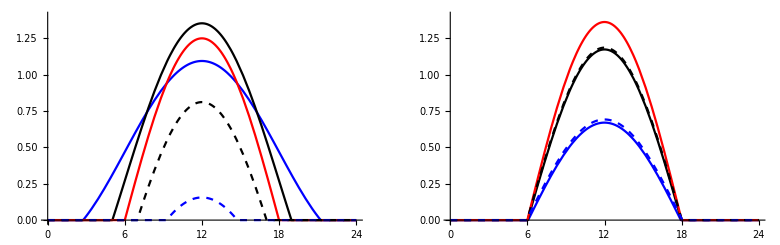

```mathematica
GraphicsRow[{fig1a,fig1b}]
```

```mathematica
(* dd = 1 min *)
DailyTemperature[J_,ϕ_,a1_,b1_,Ta0_]:=Module[{result= {},srise,sset, dd = 1/60., σ = 5.67 10^(-8) (*W/m^2 K^4 need to convert to min but it should be in b1 a1*),Ta},
srise= SunRise[J,ϕ];
sset = 12+ (12  - srise);

phase1 = Range[0,srise,dd];
phase2 = Range[srise+dd,sset,dd];
phase3 = Range[sset+dd,24+dd,dd];

s1 = NDSolve[{Ta'[t]==  -b1  σ (Ta[t]+ 273) ^4, Ta[0]==Ta0},Ta,{t,0,srise} ];
res1 = Table[Ta[t] /. s1,{t,phase1}];

(*Do a simple Euler method*)
lastTa= res1[[-1]];res2 ={};
Do[
newTa = (a1 SolarRadiation[J,tt,ϕ] - b1  σ (lastTa+ 273) ^4) dd + lastTa;
AppendTo[res2,newTa];
lastTa= newTa;
,{tt,phase2}];

s3 = NDSolve[{Ta'[t]==  -b1  σ (Ta[t]+ 273) ^4, Ta[sset+dd]==lastTa},Ta,{t,sset+dd,24+dd} ];
res3 = Table[Ta[t] /. s3,{t,phase3}];

result= Transpose[{Flatten@{phase1,phase2,phase3}, Flatten@{res1,res2,res3}}];
result];
```

```mathematica
0.00825/2
```

0.004125

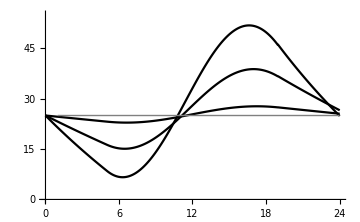

```mathematica
a1 =8; b1 =0.00825;T0 = 25; cT0=ConstantArray[T0,24];
 dt= {DailyTemperature[t1,30,a1,b1,T0],DailyTemperature[t1,30,a1/2,b1/2,T0],DailyTemperature[t1,30,a1/10,b1/10,T0],cT0};
fig1c =ListPlot[dt,Ticks->{{0,3,6,9,12,15,18,21,24},Automatic},PlotStyle->{{Black},{Black},{Black},{Gray,AbsoluteThickness[1]}},PlotRange->{All,{0,55}},Joined-> True,AxesStyle->Directive[asz,AbsoluteThickness[th],Black],ImageSize->Medium]
```

```mathematica
0.00825/750
```

0.000011

```mathematica
8*6.5
```

52.

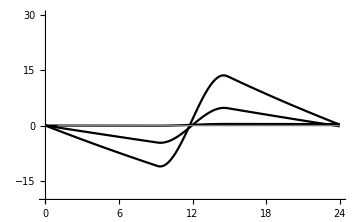

```mathematica
a1 =8; b1 =0.00825;T0 = 0; cT0=ConstantArray[T0,24];t2 = 1;
 dt= {DailyTemperature[t2,60,a1 2.5,b1/5,T0],DailyTemperature[t2,60,a1 6.5,b1/2,T0],DailyTemperature[t2,60,a1/10,b1/750,T0],cT0};
fig1d =ListPlot[dt,Ticks->{{0,3,6,9,12,15,18,21,24},Automatic},PlotStyle->{{Black},{Black},{Black},{Gray,AbsoluteThickness[1]}},PlotRange->{All,{-20,30}},AxesOrigin->{0,-20},Joined-> True,AxesStyle->Directive[asz,AbsoluteThickness[th],Black],ImageSize->Medium]
```

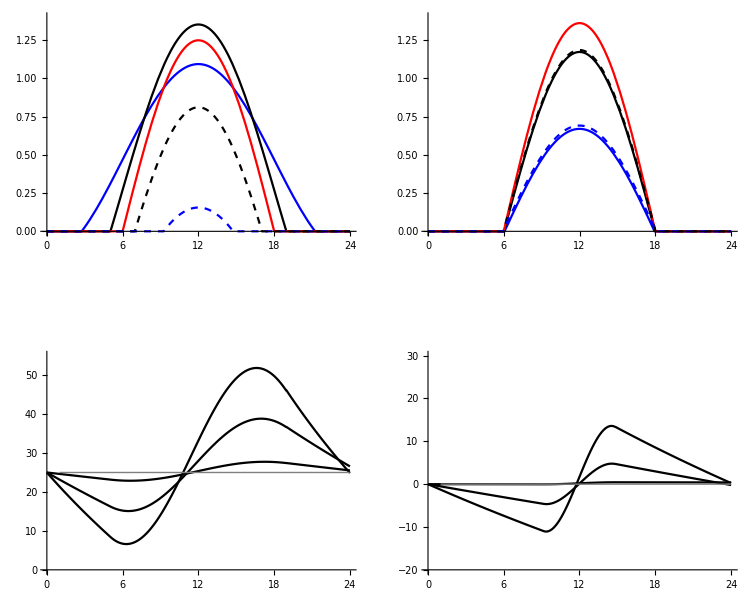

```mathematica
GraphicsGrid[{{fig1a,fig1b},{fig1c,fig1d}},Spacings-> {10,70}]
```

```mathematica
Export["C:\\Users\\tramiada\\Documents\\Projects\\1 Size and range\\10 ms\\nb\\environment.pdf",%25,"PDF"]
```

C:\Users\tramiada\Documents\Projects\1 Size and range\10 ms\nb\environment.pdf

```mathematica
a1 =5; b1 = 0.001;

J1 =1; J2 = 90; J3 = 180; J4 = 270;
T0 = 20; T1 = 10; T2 =0 ; T3 = -10;

lat = -30;
   
d1= {DailyTemperature[J1,lat,a1,b1,T0],DailyTemperature[J1,lat,a1,b1,T1],DailyTemperature[J1,lat,a1,b1,T2],DailyTemperature[J1,lat,a1,b1,T3]};
   d2= {DailyTemperature[J2,lat,a1,b1,T0],DailyTemperature[J2,lat,a1,b1,T1],DailyTemperature[J2,lat,a1,b1,T2],DailyTemperature[J2,lat,a1,b1,T3]};

d3= {DailyTemperature[J3,lat,a1,b1,T0],DailyTemperature[J3,lat,a1,b1,T1],DailyTemperature[J3,lat,a1,b1,T2],DailyTemperature[J3,lat,a1,b1,T3]};

d4= {DailyTemperature[J4,lat,a1,b1,T0],DailyTemperature[J4,lat,a1,b1,T1],DailyTemperature[J4,lat,a1,b1,T2],DailyTemperature[J4,lat,a1,b1,T3]};


f1 =ListPlot[d1,Ticks->{{0,3,6,9,12,15,18,21,24},Automatic},PlotRange->{All,{-20,50}},Joined-> True];

f2 =ListPlot[d2,Ticks->{{0,3,6,9,12,15,18,21,24},Automatic},PlotRange->{All,{-20,50}},Joined-> True];

f3 =ListPlot[d3,Ticks->{{0,3,6,9,12,15,18,21,24},Automatic},PlotRange->{All,{-20,50}},Joined-> True];

f4 =ListPlot[d4,Ticks->{{0,3,6,9,12,15,18,21,24},Automatic},PlotRange->{All,{-20,50}},Joined-> True];
```

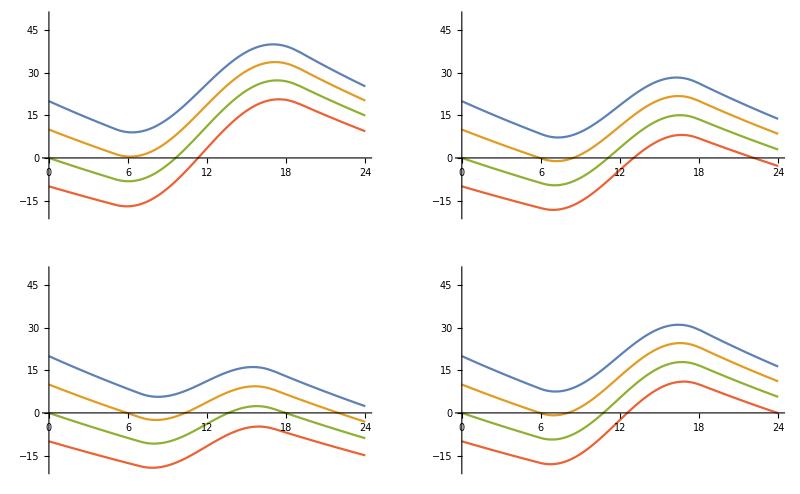

```mathematica
fig = GraphicsGrid[{{f1,f2},{f3,f4}}]
```

```mathematica
a1 =4; b1 = 0.001;

J1 =1; J2 = 90; J3 = 180; J4 = 270;
T0 = 20; T1 = 10; T2 =0 ; T3 = -10;

lat = 30;
   
d1= {DailyTemperature[J1,lat,a1,b1,T0],DailyTemperature[J1,lat,a1,b1,T1],DailyTemperature[J1,lat,a1,b1,T2],DailyTemperature[J1,lat,a1,b1,T3]};
   d2= {DailyTemperature[J2,lat,a1,b1,T0],DailyTemperature[J2,lat,a1,b1,T1],DailyTemperature[J2,lat,a1,b1,T2],DailyTemperature[J2,lat,a1,b1,T3]};

d3= {DailyTemperature[J3,lat,a1,b1,T0],DailyTemperature[J3,lat,a1,b1,T1],DailyTemperature[J3,lat,a1,b1,T2],DailyTemperature[J3,lat,a1,b1,T3]};

d4= {DailyTemperature[J4,lat,a1,b1,T0],DailyTemperature[J4,lat,a1,b1,T1],DailyTemperature[J4,lat,a1,b1,T2],DailyTemperature[J4,lat,a1,b1,T3]};


f1 =ListPlot[d1,Ticks->{{0,3,6,9,12,15,18,21,24},Automatic},PlotRange->{All,{-20,50}},Joined-> True];

f2 =ListPlot[d2,Ticks->{{0,3,6,9,12,15,18,21,24},Automatic},PlotRange->{All,{-20,50}},Joined-> True];

f3 =ListPlot[d3,Ticks->{{0,3,6,9,12,15,18,21,24},Automatic},PlotRange->{All,{-20,50}},Joined-> True];

f4 =ListPlot[d4,Ticks->{{0,3,6,9,12,15,18,21,24},Automatic},PlotRange->{All,{-20,50}},Joined-> True];
```

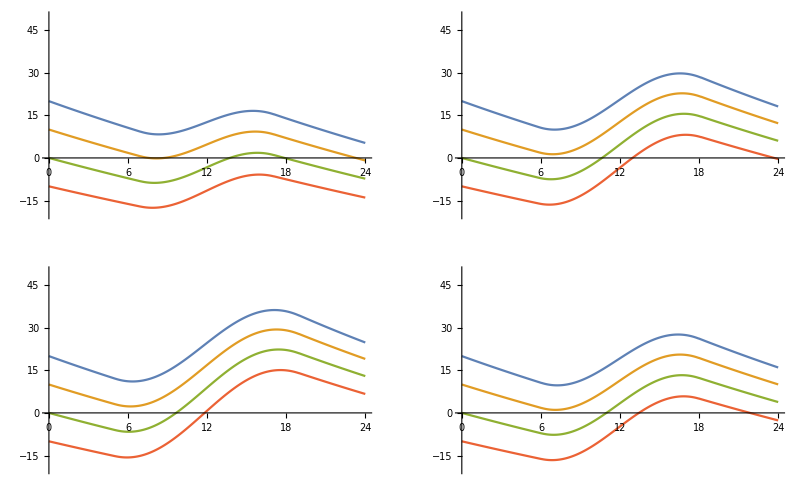

```mathematica
fig = GraphicsGrid[{{f1,f2},{f3,f4}}]
```

```mathematica
d =1.;
```

```mathematica
V = 4/3 Pi (d/2)^3
```

0.523599

```mathematica
4/3. Pi/8
```

0.523599

```mathematica
d*0.81
```

0.81

```mathematica
(V)^(1/3.)
```

0.805996